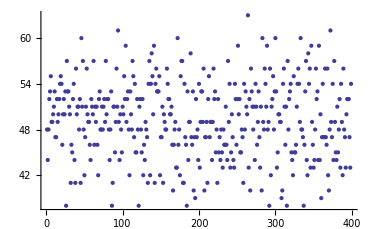

```mathematica
AA={};
For[k=1,k<400,k++,
B={};
For[j=1,j≤100,j++,
A={};
For[i=1,i≤23,i++,pa=Random[Integer,{1,12}];If[MemberQ[{1,3,5,7,8,10,12},pa],pb=Random[Integer,{1,31}],If[MemberQ[{2},pa],pb=Random[Integer,{1,28}],pb=Random[Integer,{1,30}]]];A={{pa,pb}}∪A];
B=B∪{{j,Length[A]}}];
AA=AA∪{{k,Count[B[[All,{2}]],{23}]}};
]
ListPlot[AA]
```

```mathematica
B[[All,{2}]]
B
```

{{23},{23},{23},{22},{23},{23},{22},{22},{22},{23},{22},{22},{22},{23},{22},{23},{22},{23},{22},{23},{22},{23},{22},{23},{20},{23},{22},{21},{23},{23},{22},{20},{22},{21},{23},{22},{23},{22},{22},{23},{22},{22},{22},{22},{22},{22},{22},{22},{23},{23},{22},{23},{22},{22},{23},{22},{21},{22},{22},{22},{23},{20},{23},{22},{21},{21},{23},{23},{22},{23},{22},{23},{23},{22},{23},{22},{22},{21},{21},{22},{22},{22},{23},{23},{22},{23},{22},{23},{23},{22},{23},{22},{23},{23},{23},{23},{22},{22},{23},{22}}

{{1,23},{2,23},{3,23},{4,22},{5,23},{6,23},{7,22},{8,22},{9,22},{10,23},{11,22},{12,22},{13,22},{14,23},{15,22},{16,23},{17,22},{18,23},{19,22},{20,23},{21,22},{22,23},{23,22},{24,23},{25,20},{26,23},{27,22},{28,21},{29,23},{30,23},{31,22},{32,20},{33,22},{34,21},{35,23},{36,22},{37,23},{38,22},{39,22},{40,23},{41,22},{42,22},{43,22},{44,22},{45,22},{46,22},{47,22},{48,22},{49,23},{50,23},{51,22},{52,23},{53,22},{54,22},{55,23},{56,22},{57,21},{58,22},{59,22},{60,22},{61,23},{62,20},{63,23},{64,22},{65,21},{66,21},{67,23},{68,23},{69,22},{70,23},{71,22},{72,23},{73,23},{74,22},{75,23},{76,22},{77,22},{78,21},{79,21},{80,22},{81,22},{82,22},{83,23},{84,23},{85,22},{86,23},{87,22},{88,23},{89,23},{90,22},{91,23},{92,22},{93,23},{94,23},{95,23},{96,23},{97,22},{98,22},{99,23},{100,22}}

```mathematica
Count[B[[All,{2}]],{23}]
```

49